# Report Project X

Course code: IX1501
Date: 2019-09-08 20:32

Viktor Jäger, vjager@kth.se
Sam Florin, sflorin@kth.se

Task: Winning a Teddy

## Summery

### Task

At a dice game you throw five dice in the form of the Platonic Solids. The dice are numbered with integers 1,2,…,n where n is the number of sides. The tetrahedron has its result number (1-4) written at the vertex pointing up. All other bodies have the result number on the side facing up. 
-Graphics-
At a fun-fair you can win a giant Teddy bear if you participate in the mentioned dice game. You invest €2 and then throw the five dice. If the sum S satisfies S≤10 or S≥45 you will win the Teddy. The following problems are expected to be solved by using convolution.

- Determine the exact probability function of the sum.
- Determine the exact probability of winning the Teddy prize. Also give a floating point answer.
- Determine the expected investment to win a Teddy.
- The probability of winning (at least one) Teddy if you play twenty times?

### Result

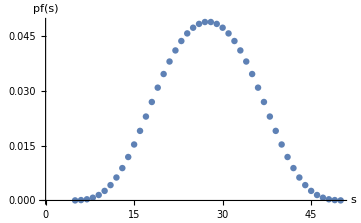
The probability function sum is determined by the probability function convolution of the individual dices.
pfSum(x)=pfd4(x)*pfd6(x)*pfd8(x)*pfd12(x)*pfd20(x) , 
where '*’ denotes convolution. The graph illustrates the probability function as a function of the five dices sum for a single dice roll.

   	-Graphics-
   	
 Determine the exact probability of winning the Teddy prize. Also give a floating point answer.
 The probability of  rolling correct sum is: 
P(S=s), 5 ≤ s ≤ 10 ∧ 45 ≥ s ≥ 50
 P(S=5)+P(S=50)= 25/4608=0,5425..%
 Determine the expected investment to win a Teddy.
 After how many times you are expected to win a Teddy is: 
1/(25/4608)=180.34
 Since the problem is Discrete we round off to 181. The roll costs 2£ which gives the investment:
181*2=362£
What’s the probability of winning (at least one) Teddy if you play twenty times?
25/4608*20=125/1152=0,1085..=10,85..%

## Method

### Probability function of the sum

### Probability of winning the Teddy

```mathematica
Yep
```

Yep

### Expected Investment

```mathematica
Yep
```

Yep

### Probability of winning several attempts

```mathematica
Yep
```

Yep

## Code

```mathematica
d4=ConstantArray[1,4]/4;
d6=ConstantArray[1,6]/6;
d8=ConstantArray[1,8]/8;
d12=ConstantArray[1,12]/12;
d20=ConstantArray[1,20]/20;
```

```mathematica
pfd4d6=ListConvolve[d4,d6,{1,-1},0];
pfd8d12=ListConvolve[d8,d12,{1,-1},0];
pfd4d6d8d12=ListConvolve[pfd4d6,pfd8d12,{1,-1},0];
pfxSum=ListConvolve[pfd4d6d8d12,d20,{1,-1},0]
```

{1/46080,1/9216,1/3072,7/9216,23/15360,121/46080,97/23040,29/4608,409/46080,61/5120,707/46080,293/15360,53/2304,311/11520,95/3072,1597/46080,39/1024,379/9216,1007/23040,211/4608,1091/23040,223/4608,1127/23040,1127/23040,223/4608,1091/23040,211/4608,1007/23040,379/9216,39/1024,1597/46080,95/3072,311/11520,53/2304,293/15360,707/46080,61/5120,409/46080,29/4608,97/23040,121/46080,23/15360,7/9216,1/3072,1/9216,1/46080}

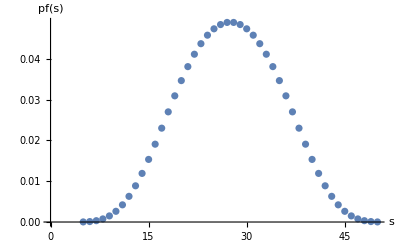

```mathematica
ListPlot[{Range[5,50],pfxSum}//Transpose,AxesLabel->{"s","pf(s)"}]
```

```mathematica
pfxS1 =Total[{1/46080,1/9216,1/3072,7/9216,23/15360, 121/46080}];
pfxS2=Total[{121/46080, 23/15360,7/9216,1/3072,1/9216,1/46080}];
```

```mathematica
PfxS1unionS2=pfxS1+pfxS2
N[PfxS1UNIONS2];
PercentForm[N[PfxS1UNIONS2]];
```

25/4608

```mathematica
expectedWin=1/PfxS1UNIONS2
```

1/PfxS1UNIONS2

```mathematica
expectedInvestment=expectedWin*2 //N
```

2./PfxS1UNIONS2